```mathematica
a1=ReadList["C:\\Users\\MI\\Desktop\\pypon\\Log5_1",Number];
a2=ReadList["C:\\Users\\MI\\Desktop\\pypon\\Log5_2.txt",Number];
a3=ReadList["C:\\Users\\MI\\Desktop\\pypon\\Log5_3.txt",Number];
a4=ReadList["C:\\Users\\MI\\Desktop\\pypon\\Log5_4.txt",Number];
a5=ReadList["C:\\Users\\MI\\Desktop\\pypon\\Log5_5.txt",Number];
c1=EmpiricalDistribution[a1];
c2=EmpiricalDistribution[a2];
c3=EmpiricalDistribution[a3];
c4=EmpiricalDistribution[a4];
c5=EmpiricalDistribution[a5];
Plot[{CDF[c1,x],CDF[c2,x],CDF[c3,x],CDF[c4,x],CDF[c5,x],CDF[LogSeriesDistribution[0.5],x]},{x,0,15}]
```

ReadList::noopen: Cannot open C:\Users\MI\Desktop\pypon\Log5_1.

EmpiricalDistribution::invldgd: The input data EmpiricalDistribution[$Failed] should be a vector or a matrix or a valid TemporalData object.

-Graphics-

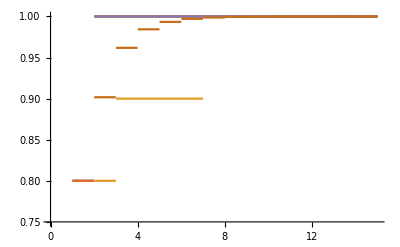

```mathematica
a1=ReadList["C:\\Users\\MI\\Desktop\\pypon\\Log10_1.txt",Number];
a2=ReadList["C:\\Users\\MI\\Desktop\\pypon\\Log10_2.txt",Number];
a3=ReadList["C:\\Users\\MI\\Desktop\\pypon\\Log10_3.txt",Number];
a4=ReadList["C:\\Users\\MI\\Desktop\\pypon\\Log10_4.txt",Number];
a5=ReadList["C:\\Users\\MI\\Desktop\\pypon\\Log10_5.txt",Number];
c1=EmpiricalDistribution[a1];
c2=EmpiricalDistribution[a2];
c3=EmpiricalDistribution[a3];
c4=EmpiricalDistribution[a4];
c5=EmpiricalDistribution[a5];
Plot[{CDF[c1,x],CDF[c2,x],CDF[c3,x],CDF[c4,x],CDF[c5,x],CDF[LogSeriesDistribution[0.5],x]},{x,0,15}]
```

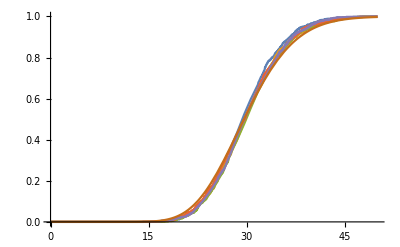

```mathematica
b1=ReadList["C:\\Users\\MI\\Desktop\\pypon\\Erl1000_1.txt",Number];
b2=ReadList["C:\\Users\\MI\\Desktop\\pypon\\Erl1000_2.txt",Number];
b3=ReadList["C:\\Users\\MI\\Desktop\\pypon\\Erl1000_3.txt",Number];
b4=ReadList["C:\\Users\\MI\\Desktop\\pypon\\Erl1000_4.txt",Number];
b5=ReadList["C:\\Users\\MI\\Desktop\\pypon\\Erl1000_5.txt",Number];
c1=EmpiricalDistribution[b1];
c2=EmpiricalDistribution[b2];
c3=EmpiricalDistribution[b3];
c4=EmpiricalDistribution[b4];
c5=EmpiricalDistribution[b5];
Plot[{CDF[c1,x],CDF[c2,x],CDF[c3,x],CDF[c4,x],CDF[c5,x],CDF[ErlangDistribution[24, 0.8],x]},{x,0,50}]
```